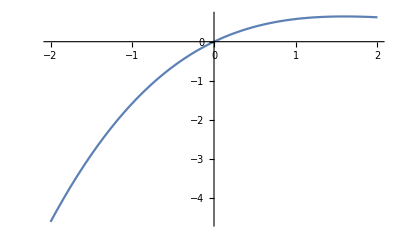

```mathematica
Plot[x^2/(Exp[x]-1),{x,-2,2}]
```

```mathematica
RX[θ_]:={
{Cos[θ/2], -ⅈ Sin[θ/2]},
{-ⅈ Sin[θ/2],Cos[θ/2]}};
RY[θ_]:={
{Cos[θ/2], -Sin[θ/2]},
{Sin[θ/2],Cos[θ/2]}};
RZ[θ_]:={
{Exp[-ⅈ θ/2],0},
{0,Exp[ⅈ θ/2]}};
Eigensystem[RX[θ]]
```

{{Cos[θ/2]-ⅈ Sin[θ/2],Cos[θ/2]+ⅈ Sin[θ/2]},{{1,1},{-1,1}}}

```mathematica
MatrixForm[FullSimplify[1/Sqrt[2]{{1,1},{-1,1}}.RX[θ].ConjugateTranspose[1/Sqrt[2]{{1,1},{-1,1}}]]]
```

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

```mathematica
VX=1/Sqrt[2]{{1,1},{-1,1}};
Z={{1,0},{0,-1}};
```

```mathematica
MatrixForm[FullSimplify[VX.RZ[θ2].RY[θ1].VX]]
```

(Cos[θ2/2] Sin[θ1/2]-ⅈ Cos[θ1/2] Sin[θ2/2] | Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2]
-Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2] | Cos[θ2/2] Sin[θ1/2]+ⅈ Cos[θ1/2] Sin[θ2/2])

```mathematica
MatrixForm[FullSimplify[VX.RY[-θ3].RZ[-θ4].Z.RZ[θ4].RY[θ3].VX]]
```

(Cos[θ3] | -Sin[θ3]
-Sin[θ3] | -Cos[θ3])

```mathematica
a[k1_,k2_,j1_,j2_]:=1/2*
ConjugateTranspose[({{Cos[θ2/2] Sin[θ1/2]-ⅈ Cos[θ1/2] Sin[θ2/2], Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2]}, {-Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2], Cos[θ2/2] Sin[θ1/2]+ⅈ Cos[θ1/2] Sin[θ2/2]}})][[k1]][[k2]]*
({{Cos[θ3], -Sin[θ3]}, {-Sin[θ3], -Cos[θ3]}})[[k2]][[j2]]*
({{Cos[θ2/2] Sin[θ1/2]-ⅈ Cos[θ1/2] Sin[θ2/2], Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2]}, {-Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2], Cos[θ2/2] Sin[θ1/2]+ⅈ Cos[θ1/2] Sin[θ2/2]}})[[j2]][[j1]]*
{1,-1}[[j1]];

(* c_{0,0} *)
Print[c_[0,0]]
FullSimplify[a[1,1,1,1]+a[2,2,2,2],+a[1,2,1,2]+a[2,1,2,1],Assumptions->θ1∈Reals&&θ2∈Reals]

(* c_{0,-1} *)
Print[c_[0,-1]]
FullSimplify[a[1,1,1,2]+a[2,1,2,2],Assumptions->θ1∈Reals&&θ2∈Reals]

(* c_{0,1} *)
Print[c_[0,1]]
FullSimplify[a[1,2,1,1]+a[2,2,2,1],Assumptions->θ1∈Reals&&θ2∈Reals]

(* c_{-1,0} *)
Print[c_[-1,0]]
FullSimplify[a[1,1,2,1]+a[1,2,2,2],Assumptions->θ1∈Reals&&θ2∈Reals]

(* c_{1,0} *)
Print[c_[1,0]]
FullSimplify[a[2,1,1,1]+a[2,2,1,2],Assumptions->θ1∈Reals&&θ2∈Reals]

(* c_{-1,-1} *)
Print[c_[-1,-1]]
FullSimplify[a[1,1,2,2],Assumptions->θ1∈Reals&&θ2∈Reals]
(* c_{1,1} *)
Print[c_[1,1]]
FullSimplify[a[2,2,1,1],Assumptions->θ1∈Reals&&θ2∈Reals]

(* c_{-1,1} *)
Print[c_[-1,1]]
FullSimplify[a[1,2,2,1],Assumptions->θ1∈Reals&&θ2∈Reals]
(* c_{1,-1} *)
Print[c_[1,-1]]
FullSimplify[a[2,1,1,2],Assumptions->θ1∈Reals&&θ2∈Reals]
```

c_[0,0]

-1/2 (-1+Cos[θ1] Cos[θ2]) Cos[θ3]

c_[0,-1]

1/2 (Sin[θ1]+ⅈ Cos[θ1] Sin[θ2]) Sin[θ3]

c_[0,1]

1/2 (Sin[θ1]-ⅈ Cos[θ1] Sin[θ2]) Sin[θ3]

c_[-1,0]

-1/2 Cos[θ3] (Cos[θ2] Sin[θ1]+ⅈ Sin[θ2])

c_[1,0]

1/2 Cos[θ3] (Cos[θ2] Sin[θ1]-ⅈ Sin[θ2])

c_[-1,-1]

1/2 (Cos[θ2/2] Sin[θ1/2]+ⅈ Cos[θ1/2] Sin[θ2/2])^2 Sin[θ3]

c_[1,1]

1/4 ⅈ (ⅈ Sin[(θ1-θ2)/2]+Sin[(θ1+θ2)/2])^2 Sin[θ3]

c_[-1,1]

-1/2 (Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2])^2 Sin[θ3]

c_[1,-1]

1/2 (Cos[θ1/2] Cos[θ2/2]-ⅈ Sin[θ1/2] Sin[θ2/2])^2 Sin[θ3]

```mathematica
TrigExpand[Sin[(θ1-θ2)/2]]
TrigExpand[Sin[(θ1+θ2)/2]]
```

Cos[θ2/2] Sin[θ1/2]-Cos[θ1/2] Sin[θ2/2]

Cos[θ2/2] Sin[θ1/2]+Cos[θ1/2] Sin[θ2/2]

```mathematica
Simplify[a[1,1,2,2],Assumptions->θ1∈Reals&&θ2∈Reals]
FullSimplify[a[1,2,2,1],Assumptions->θ1∈Reals&&θ2∈Reals]
FullSimplify[a[2,1,1,2],Assumptions->θ1∈Reals&&θ2∈Reals]
FullSimplify[a[2,2,1,1],Assumptions->θ1∈Reals&&θ2∈Reals]
```

1/2 (Cos[θ2/2] Sin[θ1/2]+ⅈ Cos[θ1/2] Sin[θ2/2])^2 Sin[θ3]

-1/2 (Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2])^2 Sin[θ3]

1/2 (Cos[θ1/2] Cos[θ2/2]-ⅈ Sin[θ1/2] Sin[θ2/2])^2 Sin[θ3]

1/4 ⅈ (ⅈ Sin[(θ1-θ2)/2]+Sin[(θ1+θ2)/2])^2 Sin[θ3]

```mathematica
TrigExpand[ⅈ Sin[(θ1-θ2)/2]+Sin[(θ1+θ2)/2]]
```

(1+ⅈ) Cos[θ2/2] Sin[θ1/2]+(1-ⅈ) Cos[θ1/2] Sin[θ2/2]

```mathematica
TeXForm[1/4 (Sin[θ1]+ⅈ Cos[θ1] Sin[θ2]) Sin[θ3]]
```

\frac{1}{4} \sin (\text{$\theta $3}) (\sin (\text{$\theta
   $1})+i \cos (\text{$\theta $1}) \sin (\text{$\theta
   $2}))